```mathematica
f[x_,y_]:=(5000-(x*x+y*y+x*y)/200+25/2*(x+y))*Exp[-Abs[0.000001*(x*x+y*y)-0.0015*(x+y)+0.7]]
```

-Graphics3D-

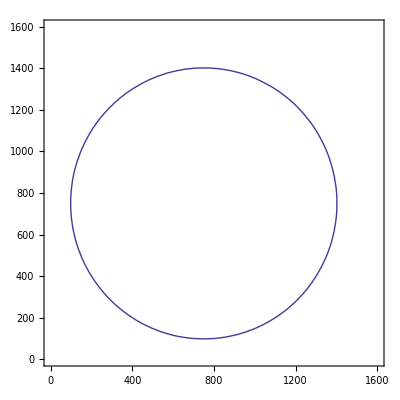

```mathematica
Plot3D[f[x,y],{x,0,1600},{y,0,1600}]
ContourPlot[0.000001*(x*x+y*y)-0.0015*(x+y)+0.7==0,{x,0,1600},{y,0,1600}]
```

```mathematica
(* solve ridge eqn for lower half of circle and sub in *)
optvl=FullSimplify[f[x,750.-1. √(-137500.+1500. x-1. x^2)]]
```

12250.-5. √(-137500.+(1500.-1. x) x)+x (1.25+0.005 √(-137500.+(1500.-1. x) x))

```mathematica
xmvl=FindMinimum[optvl,{x,500}][[2,1,2]];
ymvl=750.-1. √(-137500.+1500. x-1. x^2)/.x->xmvl;
fmin=f[xmvl,ymvl]
```

10972.6

```mathematica
(* initial height *)
hini=f[200,200];
apdis=fmin-hini;
aptofmindis=EuclideanDistance[{200,200,fmin},{xmvl,ymvl,fmin}];
fmindistobp = EuclideanDistance[{xmvl,ymvl,fmin},{1400,1400,fmin}];
aptofmindis+fmindistobp
```

1697.06

```mathematica
fmin-hini
```

3121.02

```mathematica
(* COME BACK AND MAKE SURE EVERYTHING IS ACCURATE TO 3 DECIMAL PLACES.  THEN MAKE SURE THAT WE ARE NOT FLYING THROUGH THE MOUNTAIN BY PLOTTING RESULTS*)
```